Discrete Structures

Sets

### Overview

In this section, the goal is to learn basic discrete structures.

The basis of any discrete structure is set theory.

In computer science, sets are implemented using basic data structures like arrays and queues.

In this lesson, you will learn about sets in Wolfram Language.

-Graphics-

### Definition

A set is a finite or infinite collection of elements without order and multiplicity:

```mathematica
s={1,3,9}
```

{1,3,9}

A list is an ordered set of elements:

```mathematica
{1,3,9,"a",{1,"b"},1,4}
```

{1,3,9,a,{1,b},1,4}

```mathematica
Sort@DeleteDuplicates@%
```

{1,3,4,9,a,{1,b}}

#### Size

The size of a set is the number of elements it contains:

```mathematica
Length@%
```

6

### Important Sets

Finite sets are sets of finite size {1,3,9}; infinite sets are sets of infinite size {0,0.1,0.01,0.001...}

The empty set (∅): {}

The set of integers (ℤ, Integers): {...,-3, -2, -1, 0, 1, 2, 3, ...}

The natural numbers (ℕ, NonNegativeIntegers): {0, 1, 2, 3, ...}

The rational numbers (ℚ, Rationals): {p/q | p∈ℤ ∧ q∈ℤ ∧ q≠0}

The real numbers (ℝ, Reals)

The complex numbers (ℂ, Complexes)

```mathematica
{Integers,PositiveIntegers,NegativeIntegers,NonNegativeIntegers,NonPositiveIntegers}
```

{ℤ,,,,}

### Countable and Uncountable

Any set that can be put in a one-to-one correspondence with the natural numbers is countable.

Natural numbers are by definition countable.

Integers: {0,1,-1,2,-2, 3, -3, 4, -4, ...}

Reals and complexes are uncountable.

Rationals:

```mathematica
MatrixForm[Table[p/q,{p,10},{q,10}]]
```

(1 | 1/2 | 1/3 | 1/4 | 1/5 | 1/6 | 1/7 | 1/8 | 1/9 | 1/10
2 | 1 | 2/3 | 1/2 | 2/5 | 1/3 | 2/7 | 1/4 | 2/9 | 1/5
3 | 3/2 | 1 | 3/4 | 3/5 | 1/2 | 3/7 | 3/8 | 1/3 | 3/10
4 | 2 | 4/3 | 1 | 4/5 | 2/3 | 4/7 | 1/2 | 4/9 | 2/5
5 | 5/2 | 5/3 | 5/4 | 1 | 5/6 | 5/7 | 5/8 | 5/9 | 1/2
6 | 3 | 2 | 3/2 | 6/5 | 1 | 6/7 | 3/4 | 2/3 | 3/5
7 | 7/2 | 7/3 | 7/4 | 7/5 | 7/6 | 1 | 7/8 | 7/9 | 7/10
8 | 4 | 8/3 | 2 | 8/5 | 4/3 | 8/7 | 1 | 8/9 | 4/5
9 | 9/2 | 3 | 9/4 | 9/5 | 3/2 | 9/7 | 9/8 | 1 | 9/10
10 | 5 | 10/3 | 5/2 | 2 | 5/3 | 10/7 | 5/4 | 10/9 | 1)

### Venn Diagram

Sets can be represented visually using Venn diagrams:

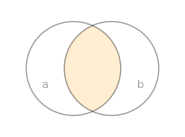

```mathematica
ResourceFunction["VennDiagram"][a∧b]
```

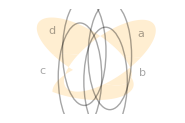

```mathematica
ResourceFunction["VennDiagram"][a⊻(b∧c∨d)]
```

### Subset

A subset (⊂, ⊆, Part) is a portion of a set:

```mathematica
{2,3,4,7,10}[[3;;4]]
```

{4,7}

#### Power Set

The power set P(S) is the set of all subsets of a set S:

```mathematica
Subsets[{2,3,4,7,10}]
```

{{},{2},{3},{4},{7},{10},{2,3},{2,4},{2,7},{2,10},{3,4},{3,7},{3,10},{4,7},{4,10},{7,10},{2,3,4},{2,3,7},{2,3,10},{2,4,7},{2,4,10},{2,7,10},{3,4,7},{3,4,10},{3,7,10},{4,7,10},{2,3,4,7},{2,3,4,10},{2,3,7,10},{2,4,7,10},{3,4,7,10},{2,3,4,7,10}}

### Partition

A set partition of a set S is a collection of disjoint subsets of S whose union is S:

```mathematica
Partition[Range[18],3]
```

{{1,2,3},{4,5,6},{7,8,9},{10,11,12},{13,14,15},{16,17,18}}

```mathematica
Partition[Range[18],4,2]
```

{{1,2,3,4},{3,4,5,6},{5,6,7,8},{7,8,9,10},{9,10,11,12},{11,12,13,14},{13,14,15,16},{15,16,17,18}}

```mathematica
Join@@%
```

{1,2,3,4,3,4,5,6,5,6,7,8,7,8,9,10,9,10,11,12,11,12,13,14,13,14,15,16,15,16,17,18}

### Cartesian Product

The Cartesian product of two sets A and B (A×B) is defined to be the set of all points such that (a ∈ A,b ∈ B):

```mathematica
Tuples[{1,3,5,7,9},2]
```

{{1,1},{1,3},{1,5},{1,7},{1,9},{3,1},{3,3},{3,5},{3,7},{3,9},{5,1},{5,3},{5,5},{5,7},{5,9},{7,1},{7,3},{7,5},{7,7},{7,9},{9,1},{9,3},{9,5},{9,7},{9,9}}

```mathematica
Tuples[{{1,3,5,7,9},{2,4}}]
```

{{1,2},{1,4},{3,2},{3,4},{5,2},{5,4},{7,2},{7,4},{9,2},{9,4}}

#### Association

An association (dictionary) is an association between keys and values:

```mathematica
<|a->x,b->y,c->z|>
```

<|a→x,b→y,c→z|>

### Dataset

A dataset is a list of structured associations of attributes and data:

```mathematica
Normal@ExampleData[{"Dataset","Titanic"}]
```

### Empty Set

Often, there is a lot of confusion about the empty set (∅, {}).

What is the size of ∅? {∅,{∅}}?

```mathematica
{Length@{},Length@{{},{{}}}}
```

{0,2}

What is the power set of ∅? What about the power set of the power set of ∅?

```mathematica
{Subsets[{}],Subsets@Subsets@{}}
```

{{{}},{{},{{}}}}

What is the Cartesian product of the empty set with any set?

```mathematica
Tuples[{{},{2,4,6,8}}]
```

{}

### Summary

Sets are the basis of discrete structures.

Important sets include ∅, ℤ, ℕ, ℚ, ℝ and ℂ.

Use Venn diagrams to easily visualize sets.

Other basic discrete structures include lists, tuples, associations and datasets.

Now that sets are clearly explained, it is time to do computations on them to fully utilize their versatility.

Download Notebook »